# Plano parámetros Newton,

```mathematica
p[z_]=(z^2-1)(z-λ); Np[z_]=z-p[z]/p'[z]//Simplify//Together
```

(2 z^3-λ-z^2 λ)/(-1+3 z^2-2 z λ)

```mathematica
Np'[z]//Simplify//Together
```

(2 (-1+z^2) (3 z^2-4 z λ+λ^2))/((-1+3 z^2-2 z λ)^2)

```mathematica
soluciones=Solve[(3 z^2-4 z λ+λ^2)==0,z]
```

{{z→λ/3},{z→λ}}

```mathematica
r0=1.;r1=-1.;r2=λ;
```

```mathematica
rootPosition := Compile[{{z,_Complex}},
    Which[Abs[z -r0] <  10.0^(-6),3,
Abs[z-r1]<10.0^(-6), 2,
Abs[z-r2]<10.0^(-6), 1,
    True, 0],
{{rootf[_],_Complex}}
]
```

```mathematica
iterSchLambda = Compile[{{z, _Complex},{ λ,_Complex}},(2 z^3-λ-z^2 λ)/(-1+3 z^2-2 z λ)]
```

CompiledFunction[…]

```mathematica
Clear[iterColorAlgorithm,colorLevel,fractalColor,plotColorFractal]
```

```mathematica
iterColorAlgorithm[iterMethod_,x_,y_,lim_] :=
    Block[{z,λ,ct,r}, z =z/.soluciones[[1]];λ= x + y I; ct = 0;r = rootPosition[z];
        While[(r==0) && (ct < lim),
            ++ct; z = iterMethod[z,λ];r = rootPosition[z]
	       ];
		    If[Head[r]==Which,r =0]; (* "Which" unevaluated Return[N[r+ct/(lim+0.001)]] *)
	       Return[N[r]]
    ]
```

```mathematica
fractalColorWS[p_] :=
Switch[IntegerPart[p],
4, RGBColor[1,1,1],
3, CMYKColor[1,0.,0.,0],
2, CMYKColor[0.,1,0.,0],
1, CMYKColor[0.,0.,1,0],
0, CMYKColor[0.,0.,0.,1.]
]
```

```mathematica
ft[min_,max_,pt_,nTicks_]:=Block[{taux,j,stepTicks=(max-min)/(nTicks-1)},
taux=Table[{pt*(j-1)/(nTicks-1)+1,min+(j-1)*stepTicks},{j,1,nTicks}]
]
```

```mathematica
plotColorFractal[iterMethod_,points_]:=
Block[{$Messages = {},
stepx=(xxMax-xxMin)/points,stepy=(yyMax-yyMin)/points},
ArrayPlot[Table[iterColorAlgorithm[iterMethod,x,y,limIterations],
{y,yyMax,1.00001*yyMin,-stepy},
{x,xxMin,1.00001*xxMax,stepx}],
FrameTicks->{ft[yyMax,yyMin,points,5],ft[xxMin,xxMax,points,5]},
PlotRange->{0,5},(* Three roots + fixed  *)
ColorFunctionScaling->False,
ColorFunction->fractalColorWS
]
]
```

```mathematica
Off[General::ovfl];    Off[General::unfl];    Off[Infinity::indet]
Off[CompiledFunction::cccx];    Off[CompiledFunction::cfn]; Off[CompiledFunction::cfcx];    Off[CompiledFunction::cfex]; Off[CompiledFunction::crcx];    Off[CompiledFunction::cfse]; Off[CompiledFunction::ilsm];    Off[CompiledFunction::cfsa]
```

```mathematica
numberPoints =512;limIterations=25;
xxMin=-4; xxMax=4; yyMin=-4; yyMax=4;plotColorFractal[iterSchLambda, numberPoints]
```

-Graphics-

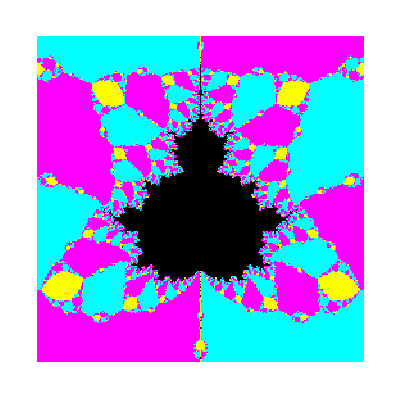

```mathematica
numberPoints =;limIterations=50;
xxMin=-0.05; xxMax=0.05; yyMin=2.9; yyMax=3;plotColorFractal[iterSchLambda, numberPoints]
```

```mathematica
2
```

```mathematica
numberPoints =512;limIterations=50;
xxMin=-0.05; xxMax=0.05; yyMin=2.9; yyMax=3;plotColorFractal[iterSchLambda, numberPoints]
```

-Graphics-